Vaccum ultraviolet optical properties of LAr for DM and neu exp

```mathematica
(*gas argon Sellmeier Expression*)

l1 = √(1/91.012)*1000
l2 = √(1/87.892)*1000
l3 = √(1/214.02)*1000
```

104.822

106.666

68.3554

```mathematica
n[x_] := 1 + 1.2055/100*(0.2075/(91.012-x^-2) + 0.0415/(87.892-x^-2)+4.3330/(214.02-x^-2))
```

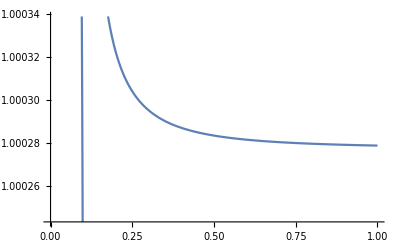

```mathematica
Plot[n[x], {x, 0, 1}]
```

```mathematica
(*Liquid argon extrapolation*)
```

```mathematica
nl[x_]:= √(3/(1-1.2055/100*2/3*(34.93/(44.66/1000))*(0.2075/(91.012-x^-2) + 0.0415/(89.892-x^-2)+4.3330/(214.02-x^-2)))-2)
```

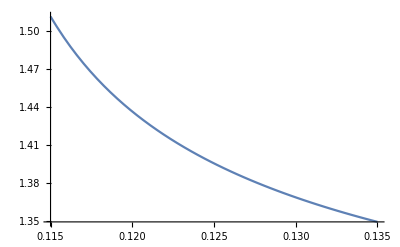

```mathematica
Plot[nl[x], {x, 0.115, 0.135}]
```

```mathematica
nl[0.128]
```

1.37806

```mathematica
1.378058394616343
```

```mathematica
NA = 6.022
```

6.022

```mathematica
(*Wannier excitons*)
```

```mathematica
nl1[x_]:=√(3/(1-1.2055/100*2/3*((24.8*10000)/(44.66*NA))*(0.227/((0.1015)^-2-x^-2) + 0.035/((0.1037)^-2-x^-2)+4.3330/(214.02-x^-2)))-2)
```

```mathematica
nl1[0.128]
```

1.44222

```mathematica
nl2[x_]:=√(3/(1-1.2055/100*2/3*((21.1*10000)/(44.66*NA))*(0.207/((0.1029)^-2-x^-2) + 0.054/((0.1052)^-2-x^-2)+4.3330/(214.02-x^-2)))-2)
```

```mathematica
nl2[0.128]
```

1.37564

```mathematica
nl3[x_]:=√(3/(1-1.2055/100*2/3*((19.5*10000)/(44.66*NA))*(0.167/((0.1035)^-2-x^-2) + 0.063/((0.1057)^-2-x^-2)+4.3330/(214.02-x^-2)))-2)
```

```mathematica
nl3[0.128]
```

1.3372

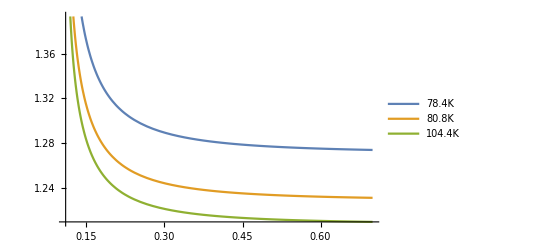

```mathematica
Plot[{nl1[x], nl2[x], nl3[x]}, {x, 0.11, 0.7}, PlotLegends->{"78.4K", "80.8K", "104.4K"}]
```

```mathematica
(*Calculation and Experiments: 1969 experiment --> 83.81K*)
```

```mathematica
ncalc1[x_] := √(3/(1-1.2055/100*2/3*(35.49/(44.66*10^-3))*(0.227/((0.1015)^-2-(x)^-2) + 0.035/((0.1037)^-2-(x)^-2)+4.3330/(214.02-(x)^-2)))-2)
```

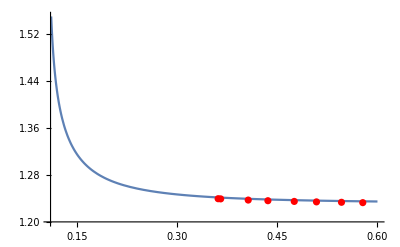

```mathematica
Show[Plot[ncalc1[x],{x, 0.11, 0.6},PlotRange->{{0.11, 0.6}, {1.2, 1.55}}],  ListPlot[{{0.3612,1.2395}, {0.365,1.2392}, {0.4063,1.2372}, {0.4358,1.2361}, {0.4753,1.2349}, {0.5086,1.2341}, {0.5461,1.2334}, {0.578,1.2328}, {0.6439,1.232}}, PlotStyle->{Red}]]
```

```mathematica
ncalc1[0.128]
```

1.37353

;

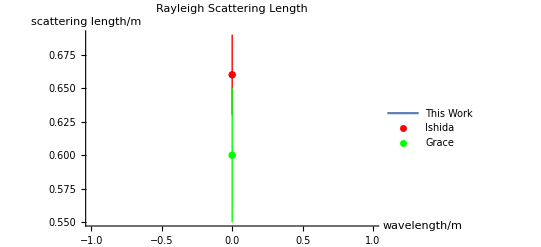

```mathematica
(*Rayleigh scattering length*);
kT = 2.18*10^-9;
kB = 1.380649*10^-23   ; 
T = 87.3;
Lray[x_] := 1/((8*Pi^3)/(3*x^4) *(((ncalc1[x]*ncalc1[x]-1)*(ncalc1[x]*ncalc1[x]+2))/3)^2*kB*T*kT);
plt1 = Plot[Lray[x], {x, 1.2*10^-7, 1.3*10^-7}, PlotLabel->"Rayleigh Scattering Length", AxesLabel->{"wavelength/m", "scattering length/m"}, PlotLegends->{"This Work"}];
plt2 = ListPlot[{{128*10^-9,Around[0.66, 0.03]}}, PlotStyle->{Red}, PlotLegends->{"Ishida"}];
plt3 = ListPlot[{{128*10^-9,Around[0.60, 0.05]}}, PlotStyle->{Green}, PlotLegends->{"Grace"}];
Show[plt1,plt2, plt3]
```

```mathematica
Lray[128*10^-9]
```

11.1201/((ncalc1[x]*ncalc1[x]-1)*(ncalc1[x]*ncalc1[x]+2))^2

```mathematica
(*Longer  Rayleigh scattering length indicateds that there might be absorption in LAr due to impurities.*)

(*Transimission of LAr*)
```